```mathematica
QFT I-Part I:Section 1.1
```

```mathematica
<<FeynArts`

InitializeModel["Phi4"]
```

FeynArts 3.12 (27 Mar 2025)

(patched for use with FeynCalc) by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

loading generic model file C:\Users\SaBa User\AppData\Roaming\Wolfram\Applications\FeynArts\Models\Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

InitializeModel::noopen: Cannot open Phi4.mod.

$Aborted

```mathematica
modelDir="C:\\Users\\SaBa User\\AppData\\Roaming\\Wolfram\\Applications\\FeynArts\\Models";

FileNames["Phi4*",modelDir]
```

{}

```mathematica
FileExistsQ[FileNameJoin[{modelDir,"Phi4.mod"}]]
```

False

```mathematica
modelDir=FileNameJoin[{$UserBaseDirectory,"Applications","FeynArts","Models"}];

phi4Content="
M$ClassesDescription = {
  S[1] == {
    SelfConjugate -> True,
    Mass -> m,
    PropagatorLabel -> \"phi\",
    PropagatorType -> ScalarDash,
    PropagatorArrow -> None
  }
};

M$CouplingMatrices = {
  C[S[1], S[1], S[1], S[1]] == {{-I lambda}}
};

M$LastModelRules = {};
";

Export[FileNameJoin[{modelDir,"Phi4.mod"}],phi4Content,"Text"]
```

C:\Users\SaBa User\AppData\Roaming\Wolfram\Applications\FeynArts\Models\Phi4.mod

```mathematica
FileExistsQ[FileNameJoin[{modelDir,"Phi4.mod"}]]
```

True

```mathematica
<<FeynArts`
InitializeModel["Phi4"]
```

FeynArts 3.12 (27 Mar 2025)

(patched for use with FeynCalc) by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

loading generic model file C:\Users\SaBa User\AppData\Roaming\Wolfram\Applications\FeynArts\Models\Lorentz.gen

FeynArts 3.12 (27 Mar 2025)

(patched for use with FeynCalc) by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

loading generic model file C:\Users\SaBa User\AppData\Roaming\Wolfram\Applications\FeynArts\Models\Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file C:\Users\SaBa User\AppData\Roaming\Wolfram\Applications\FeynArts\Models\Phi4.mod

> 1 particles (incl. antiparticles) in 1 classes

> $CounterTerms are ON

> 1 vertices

classes model {Phi4} initialized

inserting at level(s) {Classes}

> Top. 1: 1 Classes insertion

> Top. 2: 0 Classes insertions

in total: 1 Classes insertion

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 0 Classes insertions

> Top. 3: 0 Classes insertions

> Top. 4: 0 Classes insertions

> Top. 5: 0 Classes insertions

> Top. 6: 0 Classes insertions

> Top. 7: 0 Classes insertions

> Top. 8: 0 Classes insertions

> Top. 9: 0 Classes insertions

> Top. 10: 1 Classes insertion

> Top. 11: 1 Classes insertion

> Top. 12: 1 Classes insertion

in total: 3 Classes insertions

> Top. 1 ac\bc\cc.m, 0 diagrams

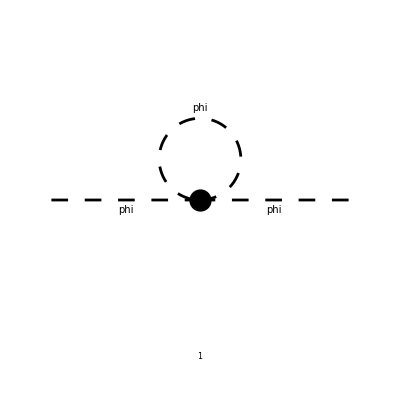

> Top. 1 aebe\cfdf\efef.m, 0 diagrams

> Top. 2 aebf\cedf\efef.m, 0 diagrams

> Top. 3 aebf\cfde\efef.m, 0 diagrams

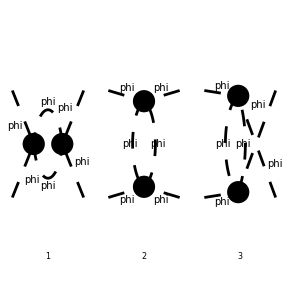

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

in total: 1 Classes amplitude

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

> Top. 2: 1 Classes amplitude

> Top. 3: 1 Classes amplitude

in total: 3 Classes amplitudes

Contract(FCI(FCFAConvert(FAFeynAmpList(Process→(S(1) | p1 | m | {})→(S(1) | k1 | m | {}),Model→{Phi4},GenericModel→{Lorentz},AmplitudeLevel→{Classes},ExcludeParticles→{},ExcludeFieldPoints→{},LastSelections→{})(FAFeynAmp(GraphID(Topology==1,Generic==1,Classes==1,Number==1),Integral[q1],1/2 lambda FAFeynAmpDenominator(1/((q1)^2-m^2)))),IncomingMomenta→{p},OutgoingMomenta→{p},LoopMomenta→{q},ChangeDimension→d,List→False)))

Contract(FCI(FCFAConvert(FAFeynAmpList(Process→(S(1) | p1 | m | {}
S(1) | p2 | m | {})→(S(1) | k1 | m | {}
S(1) | k2 | m | {}),Model→{Phi4},GenericModel→{Lorentz},AmplitudeLevel→{Classes},ExcludeParticles→{},ExcludeFieldPoints→{},LastSelections→{})(FAFeynAmp(GraphID(Topology==1,Generic==1,Classes==1,Number==1),Integral[q1],1/2 lambda^2 FAFeynAmpDenominator(1/((q1)^2-m^2),1/((-k1-k2+q1)^2-m^2))),FAFeynAmp(GraphID(Topology==2,Generic==1,Classes==1,Number==2),Integral[q1],1/2 lambda^2 FAFeynAmpDenominator(1/((q1)^2-m^2),1/((-k2+p2+q1)^2-m^2))),FAFeynAmp(GraphID(Topology==3,Generic==1,Classes==1,Number==3),Integral[q1],1/2 lambda^2 FAFeynAmpDenominator(1/((q1)^2-m^2),1/((-k1+p2+q1)^2-m^2)))),IncomingMomenta→{p1,p2},OutgoingMomenta→{p3,p4},LoopMomenta→{q},ChangeDimension→d,List→False)))

```mathematica
(*Load packages*)<<FeynArts`


(*Generate only 1PI one-loop topologies*)
top2=CreateTopologies[1,1->1,ExcludeTopologies->Internal];

top4=CreateTopologies[1,2->2,ExcludeTopologies->Internal];

(*Insert the real scalar field*)
diag2=InsertFields[top2,{S[1]}->{S[1]},Model->"Phi4",InsertionLevel->{Classes}];

diag4=InsertFields[top4,{S[1],S[1]}->{S[1],S[1]},Model->"Phi4",InsertionLevel->{Classes}];

(*Display diagrams*)
Paint[diag2,Numbering->Simple];
Paint[diag4,Numbering->Simple];


(*Generate FeynArts amplitudes*)
faAmp2=CreateFeynAmp[diag2,Truncated->True,PreFactor->1];

faAmp4=CreateFeynAmp[diag4,Truncated->True,PreFactor->1];

(*Convert to FeynCalc notation*)
amp2=FCFAConvert[faAmp2,IncomingMomenta->{p},OutgoingMomenta->{p},LoopMomenta->{q},ChangeDimension->d,List->False];

amp4=FCFAConvert[faAmp4,IncomingMomenta->{p1,p2},OutgoingMomenta->{p3,p4},LoopMomenta->{q},ChangeDimension->d,List->False];

(*Replace model parameters,if the model uses these names*)
amp2=amp2/. {Mphi->m,g->lambda};
amp4=amp4/. {Mphi->m,g->lambda};

(*Show the converted integrands*)
amp2//FCI//Contract
amp4//FCI//Contract
```

```mathematica
(*One-loop 1PI topologies*)top2=CreateTopologies[1,1->1,ExcludeTopologies->Internal];

top4=CreateTopologies[1,2->2,ExcludeTopologies->Internal];

(*Insert scalar fields*)
diag2=InsertFields[top2,{S[1]}->{S[1]},Model->"Phi4",InsertionLevel->{Classes}];

diag4=InsertFields[top4,{S[1],S[1]}->{S[1],S[1]},Model->"Phi4",InsertionLevel->{Classes}];

(*Draw diagrams*)
Paint[diag2,Numbering->Simple];
Paint[diag4,Numbering->Simple];

(*Generate amplitudes*)
faAmp2=CreateFeynAmp[diag2,Truncated->True,PreFactor->1];

faAmp4=CreateFeynAmp[diag4,Truncated->True,PreFactor->1];

(*Convert to FeynCalc notation*)
amp2=FCFAConvert[faAmp2,IncomingMomenta->{p},OutgoingMomenta->{p},LoopMomenta->{q},ChangeDimension->d,List->False];

amp4=FCFAConvert[faAmp4,IncomingMomenta->{p1,p2},OutgoingMomenta->{p3,p4},LoopMomenta->{q},ChangeDimension->d,List->False];

(*Display converted amplitudes*)
amp2
amp4
```

inserting at level(s) {Classes}

> Top. 1: 1 Classes insertion

> Top. 2: 0 Classes insertions

in total: 1 Classes insertion

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 0 Classes insertions

> Top. 3: 0 Classes insertions

> Top. 4: 0 Classes insertions

> Top. 5: 0 Classes insertions

> Top. 6: 0 Classes insertions

> Top. 7: 0 Classes insertions

> Top. 8: 0 Classes insertions

> Top. 9: 0 Classes insertions

> Top. 10: 1 Classes insertion

> Top. 11: 1 Classes insertion

> Top. 12: 1 Classes insertion

in total: 3 Classes insertions

> Top. 1 ac\bc\cc.m, 0 diagrams

-Graphics-

> Top. 1 aebe\cfdf\efef.m, 0 diagrams

> Top. 2 aebf\cedf\efef.m, 0 diagrams

> Top. 3 aebf\cfde\efef.m, 0 diagrams

-Graphics-

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

in total: 1 Classes amplitude

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

> Top. 2: 1 Classes amplitude

> Top. 3: 1 Classes amplitude

in total: 3 Classes amplitudes

FCFAConvert(FAFeynAmpList(Process→(S(1) | p1 | m | {})→(S(1) | k1 | m | {}),Model→{Phi4},GenericModel→{Lorentz},AmplitudeLevel→{Classes},ExcludeParticles→{},ExcludeFieldPoints→{},LastSelections→{})(FAFeynAmp(GraphID(Topology==1,Generic==1,Classes==1,Number==1),Integral[q1],1/2 lambda FAFeynAmpDenominator(1/((q1)^2-m^2)))),IncomingMomenta→{p},OutgoingMomenta→{p},LoopMomenta→{q},ChangeDimension→d,List→False)

FCFAConvert(FAFeynAmpList(Process→(S(1) | p1 | m | {}
S(1) | p2 | m | {})→(S(1) | k1 | m | {}
S(1) | k2 | m | {}),Model→{Phi4},GenericModel→{Lorentz},AmplitudeLevel→{Classes},ExcludeParticles→{},ExcludeFieldPoints→{},LastSelections→{})(FAFeynAmp(GraphID(Topology==1,Generic==1,Classes==1,Number==1),Integral[q1],1/2 lambda^2 FAFeynAmpDenominator(1/((q1)^2-m^2),1/((-k1-k2+q1)^2-m^2))),FAFeynAmp(GraphID(Topology==2,Generic==1,Classes==1,Number==2),Integral[q1],1/2 lambda^2 FAFeynAmpDenominator(1/((q1)^2-m^2),1/((-k2+p2+q1)^2-m^2))),FAFeynAmp(GraphID(Topology==3,Generic==1,Classes==1,Number==3),Integral[q1],1/2 lambda^2 FAFeynAmpDenominator(1/((q1)^2-m^2),1/((-k1+p2+q1)^2-m^2)))),IncomingMomenta→{p1,p2},OutgoingMomenta→{p3,p4},LoopMomenta→{q},ChangeDimension→d,List→False)

```mathematica
(*One-loop 1PI topologies*)top2=CreateTopologies[1,1->1,ExcludeTopologies->Internal];

top4=CreateTopologies[1,2->2,ExcludeTopologies->Internal];

(*Insert scalar fields*)
diag2=InsertFields[top2,{S[1]}->{S[1]},Model->"Phi4",InsertionLevel->{Classes}];

diag4=InsertFields[top4,{S[1],S[1]}->{S[1],S[1]},Model->"Phi4",InsertionLevel->{Classes}];

(*Draw diagrams*)
Paint[diag2,Numbering->Simple];
Paint[diag4,Numbering->Simple];

(*Generate amplitudes*)
faAmp2=CreateFeynAmp[diag2,Truncated->True,PreFactor->1];

faAmp4=CreateFeynAmp[diag4,Truncated->True,PreFactor->1];

(*Convert to FeynCalc notation*)
amp2=FCFAConvert[faAmp2,IncomingMomenta->{p},OutgoingMomenta->{p},LoopMomenta->{q},ChangeDimension->d,List->False];

amp4=FCFAConvert[faAmp4,IncomingMomenta->{p1,p2},OutgoingMomenta->{p3,p4},LoopMomenta->{q},ChangeDimension->d,List->False];

(*Display converted amplitudes*)
amp2
amp4
```

inserting at level(s) {Classes}

> Top. 1: 1 Classes insertion

> Top. 2: 0 Classes insertions

in total: 1 Classes insertion

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 0 Classes insertions

> Top. 3: 0 Classes insertions

> Top. 4: 0 Classes insertions

> Top. 5: 0 Classes insertions

> Top. 6: 0 Classes insertions

> Top. 7: 0 Classes insertions

> Top. 8: 0 Classes insertions

> Top. 9: 0 Classes insertions

> Top. 10: 1 Classes insertion

> Top. 11: 1 Classes insertion

> Top. 12: 1 Classes insertion

in total: 3 Classes insertions

> Top. 1 ac\bc\cc.m, 0 diagrams

-Graphics-

> Top. 1 aebe\cfdf\efef.m, 0 diagrams

> Top. 2 aebf\cedf\efef.m, 0 diagrams

> Top. 3 aebf\cfde\efef.m, 0 diagrams

-Graphics-

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

in total: 1 Classes amplitude

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

> Top. 2: 1 Classes amplitude

> Top. 3: 1 Classes amplitude

in total: 3 Classes amplitudes

FCFAConvert(FAFeynAmpList(Process→(S(1) | p1 | m | {})→(S(1) | k1 | m | {}),Model→{Phi4},GenericModel→{Lorentz},AmplitudeLevel→{Classes},ExcludeParticles→{},ExcludeFieldPoints→{},LastSelections→{})(FAFeynAmp(GraphID(Topology==1,Generic==1,Classes==1,Number==1),Integral[q1],1/2 lambda FAFeynAmpDenominator(1/((q1)^2-m^2)))),IncomingMomenta→{p},OutgoingMomenta→{p},LoopMomenta→{q},ChangeDimension→d,List→False)

FCFAConvert(FAFeynAmpList(Process→(S(1) | p1 | m | {}
S(1) | p2 | m | {})→(S(1) | k1 | m | {}
S(1) | k2 | m | {}),Model→{Phi4},GenericModel→{Lorentz},AmplitudeLevel→{Classes},ExcludeParticles→{},ExcludeFieldPoints→{},LastSelections→{})(FAFeynAmp(GraphID(Topology==1,Generic==1,Classes==1,Number==1),Integral[q1],1/2 lambda^2 FAFeynAmpDenominator(1/((q1)^2-m^2),1/((-k1-k2+q1)^2-m^2))),FAFeynAmp(GraphID(Topology==2,Generic==1,Classes==1,Number==2),Integral[q1],1/2 lambda^2 FAFeynAmpDenominator(1/((q1)^2-m^2),1/((-k2+p2+q1)^2-m^2))),FAFeynAmp(GraphID(Topology==3,Generic==1,Classes==1,Number==3),Integral[q1],1/2 lambda^2 FAFeynAmpDenominator(1/((q1)^2-m^2),1/((-k1+p2+q1)^2-m^2)))),IncomingMomenta→{p1,p2},OutgoingMomenta→{p3,p4},LoopMomenta→{q},ChangeDimension→d,List→False)

```mathematica
amp2
```

FCFAConvert(FAFeynAmpList(Process→(S(1) | p1 | m | {})→(S(1) | k1 | m | {}),Model→{Phi4},GenericModel→{Lorentz},AmplitudeLevel→{Classes},ExcludeParticles→{},ExcludeFieldPoints→{},LastSelections→{})(FAFeynAmp(GraphID(Topology==1,Generic==1,Classes==1,Number==1),Integral[q1],1/2 lambda FAFeynAmpDenominator(1/((q1)^2-m^2)))),IncomingMomenta→{p},OutgoingMomenta→{p},LoopMomenta→{q},ChangeDimension→d,List→False)

```mathematica
amp4
```

FCFAConvert(FAFeynAmpList(Process→(S(1) | p1 | m | {}
S(1) | p2 | m | {})→(S(1) | k1 | m | {}
S(1) | k2 | m | {}),Model→{Phi4},GenericModel→{Lorentz},AmplitudeLevel→{Classes},ExcludeParticles→{},ExcludeFieldPoints→{},LastSelections→{})(FAFeynAmp(GraphID(Topology==1,Generic==1,Classes==1,Number==1),Integral[q1],1/2 lambda^2 FAFeynAmpDenominator(1/((q1)^2-m^2),1/((-k1-k2+q1)^2-m^2))),FAFeynAmp(GraphID(Topology==2,Generic==1,Classes==1,Number==2),Integral[q1],1/2 lambda^2 FAFeynAmpDenominator(1/((q1)^2-m^2),1/((-k2+p2+q1)^2-m^2))),FAFeynAmp(GraphID(Topology==3,Generic==1,Classes==1,Number==3),Integral[q1],1/2 lambda^2 FAFeynAmpDenominator(1/((q1)^2-m^2),1/((-k1+p2+q1)^2-m^2)))),IncomingMomenta→{p1,p2},OutgoingMomenta→{p3,p4},LoopMomenta→{q},ChangeDimension→d,List→False)

```mathematica
Head[amp2]
Head[amp4]
```

FCFAConvert

FCFAConvert

```mathematica
Context[FCFAConvert]
```

Global`

```mathematica
Length[DownValues[FCFAConvert]]
```

0

```mathematica
Names["FeynCalc`FCFAConvert"]
```

{}

```mathematica
$LoadAddOns = {"FeynArts"};

<< FeynCalc`
```

FeynCalc is already loaded! If you are trying to reload FeynCalc or load FeynArts, TARCER, PHI, FeynHelpers or any other add-on, please restart the kernel.

$Aborted

```mathematica
$LoadAddOns={"FeynArts"};

<<FeynCalc`
```

FeynCalc 10.2.1 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

General::noopen: Cannot open C:\Users\SaBa User\AppData\Roaming\Wolfram\Applications\FeynCalc\FeynArts\FeynArts.m.

FeynCalc::faerror: FeynArts not found or damaged. Please download the FeynArts tarball from www.feynarts.de, unpack it to C:\Users\SaBa User\AppData\Roaming\Wolfram\Applications\FeynCalc\FeynArts and restart FeynCalc.

Get::noopen: Cannot open C:\Users\SaBa User\AppData\Roaming\Wolfram\Applications\FeynCalc\FeynArts\FeynArts.m.

FeynCalc::faerror: FeynArts not found or damaged. Please download the FeynArts tarball from www.feynarts.de, unpack it to C:\Users\SaBa User\AppData\Roaming\Wolfram\Applications\FeynCalc\FeynArts and restart FeynCalc.

```mathematica
faSource=FileNameJoin[{$UserBaseDirectory,"Applications","FeynArts"}];

faTarget=FileNameJoin[{$UserBaseDirectory,"Applications","FeynCalc","FeynArts"}];
```

```mathematica
{FileExistsQ[FileNameJoin[{faSource,"FeynArts.m"}]],FileExistsQ[FileNameJoin[{faSource,"Models","Phi4.mod"}]]}
```

{True,True}

```mathematica
If[!DirectoryQ[faTarget],CopyDirectory[faSource,faTarget]]
```

C:\Users\SaBa User\AppData\Roaming\Wolfram\Applications\FeynCalc\FeynArts

```mathematica
{FileExistsQ[FileNameJoin[{faTarget,"FeynArts.m"}]],FileExistsQ[FileNameJoin[{faTarget,"Models","Phi4.mod"}]]}
```

{True,True}

```mathematica
$LoadAddOns={"FeynArts"};
<<FeynCalc`
```

FeynCalc 10.2.1 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (27 Mar 2025) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

```mathematica
Names["FeynCalc`FCFAConvert"]
```

{FCFAConvert}

```mathematica
Context[FCFAConvert]
```

FeynCalc`

```mathematica
amp2=FCFAConvert[faAmp2,IncomingMomenta->{p},OutgoingMomenta->{p},LoopMomenta->{q},ChangeDimension->d,List->False];

amp4=FCFAConvert[faAmp4,IncomingMomenta->{p1,p2},OutgoingMomenta->{p3,p4},LoopMomenta->{q},ChangeDimension->d,List->False];
```

```mathematica
amp2
amp4
```

FCFAConvert(faAmp2,IncomingMomenta→{p},OutgoingMomenta→{p},LoopMomenta→{q},ChangeDimension→d,List→False)

FCFAConvert(faAmp4,IncomingMomenta→{p1,p2},OutgoingMomenta→{p3,p4},LoopMomenta→{q},ChangeDimension→d,List→False)

```mathematica
ValueQ[faAmp2]
ValueQ[faAmp4]
```

False

False

```mathematica
(*Generate topologies*)top2=CreateTopologies[1,1->1,ExcludeTopologies->Internal];

top4=CreateTopologies[1,2->2,ExcludeTopologies->Internal];

(*Insert fields*)
diag2=InsertFields[top2,{S[1]}->{S[1]},Model->"Phi4",InsertionLevel->{Classes}];

diag4=InsertFields[top4,{S[1],S[1]}->{S[1],S[1]},Model->"Phi4",InsertionLevel->{Classes}];

(*Generate amplitudes*)
faAmp2=CreateFeynAmp[diag2,Truncated->True,PreFactor->1];

faAmp4=CreateFeynAmp[diag4,Truncated->True,PreFactor->1];
```

loading generic model file C:\Users\SaBa User\AppData\Roaming\Wolfram\Applications\FeynCalc\FeynArts\Models\Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file C:\Users\SaBa User\AppData\Roaming\Wolfram\Applications\FeynCalc\FeynArts\Models\Phi4.mod

> 1 particles (incl. antiparticles) in 1 classes

> $CounterTerms are ON

> 1 vertices

classes model {Phi4} initialized

inserting at level(s) {Classes}

> Top. 1: 1 Classes insertion

> Top. 2: 0 Classes insertions

in total: 1 Classes insertion

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 0 Classes insertions

> Top. 3: 0 Classes insertions

> Top. 4: 0 Classes insertions

> Top. 5: 0 Classes insertions

> Top. 6: 0 Classes insertions

> Top. 7: 0 Classes insertions

> Top. 8: 0 Classes insertions

> Top. 9: 0 Classes insertions

> Top. 10: 1 Classes insertion

> Top. 11: 1 Classes insertion

> Top. 12: 1 Classes insertion

in total: 3 Classes insertions

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

in total: 1 Classes amplitude

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

> Top. 2: 1 Classes amplitude

> Top. 3: 1 Classes amplitude

in total: 3 Classes amplitudes

```mathematica
amp2=FCFAConvert[faAmp2,IncomingMomenta->{p},OutgoingMomenta->{p},LoopMomenta->{q},ChangeDimension->d,List->False];

amp4=FCFAConvert[faAmp4,IncomingMomenta->{p1,p2},OutgoingMomenta->{p3,p4},LoopMomenta->{q},ChangeDimension->d,List->False];
```

```mathematica
amp2
amp4
```

lambda/(2 (q^2-m^2))

lambda^2/(2 (q^2-m^2).((p2-p3+q)^2-m^2))+lambda^2/(2 (q^2-m^2).((p2-p4+q)^2-m^2))+lambda^2/(2 (q^2-m^2).((-p3-p4+q)^2-m^2))

```mathematica
(*Define the three channel momenta*)kS=p1+p2;
kT=p1-p3;
kU=p1-p4;

(*Define the three bubble integrands*)
bubbleS=1/((q^2-m^2) ((q-kS)^2-m^2));

bubbleT=1/((q^2-m^2) ((q+kT)^2-m^2));

bubbleU=1/((q^2-m^2) ((q+kU)^2-m^2));

(*Display the integrands*)
{bubbleS,bubbleT,bubbleU}
```

{1/((q^2-m^2) ((-p1-p2+q)^2-m^2)),1/((q^2-m^2) ((p1-p3+q)^2-m^2)),1/((q^2-m^2) ((p1-p4+q)^2-m^2))}

```mathematica
(*Two-point function:tadpole integral*)tadpoleFAD=FAD[{q,m}];

(*Convert to Passarino-Veltman form*)
tadpolePV=ToPaVe[tadpoleFAD,q];

tadpolePV
```

ⅈ π^2 A_0(m^2)

```mathematica
(*Define the three channel momenta*)kS=p1+p2;
kT=p1-p3;
kU=p1-p4;

(*Construct the FeynCalc propagator denominators*)
bubbleSFAD=FAD[{q,m},{q-kS,m}];
bubbleTFAD=FAD[{q,m},{q+kT,m}];
bubbleUFAD=FAD[{q,m},{q+kU,m}];

(*Convert each bubble to Passarino-Veltman form*)
bubbleSPV=ToPaVe[bubbleSFAD,q];
bubbleTPV=ToPaVe[bubbleTFAD,q];
bubbleUPV=ToPaVe[bubbleUFAD,q];

(*Display the results*)
{bubbleSPV,bubbleTPV,bubbleUPV}
```

{ⅈ π^2 B_0(p1^2+2 (p1·p2)+p2^2,m^2,m^2),ⅈ π^2 B_0(p1^2-2 (p1·p3)+p3^2,m^2,m^2),ⅈ π^2 B_0(p1^2-2 (p1·p4)+p4^2,m^2,m^2)}

```mathematica
(*Mandelstam variables*)s=SP[p1+p2,p1+p2];
t=SP[p1-p3,p1-p3];
u=SP[p1-p4,p1-p4];

(*Compact Passarino-Veltman results*)
tadpoleResult=A0[m^2];

bubbleResults={B0[s,m^2,m^2],B0[t,m^2,m^2],B0[u,m^2,m^2]};

{tadpoleResult,bubbleResults}
```

{A_0(m^2),{B_0((OverBar[p1]+OverBar[p2])^2,m^2,m^2),B_0((OverBar[p1]-OverBar[p3])^2,m^2,m^2),B_0((OverBar[p1]-OverBar[p4])^2,m^2,m^2)}}

```mathematica
### Wick Rotation and Loop-Measure Conventions

The amplitudes generated by FeynArts are initially expressed using Minkowski propagator denominators of the form
\[
\frac{1}{q_M^2-m^2+i0}.
\]
However,the action considered in this problem is Euclidean.We therefore perform a Wick rotation of the loop-energy integration:\[q^0=iq_4,\qquad q_M^2=-q_E^2,\qquad d^Dq_M=i\,d^Dq_E.
\]
The propagator denominator consequently becomes
\[q_M^2-m^2+i0\longrightarrow-(q_E^2+m^2).
\]
All factors of \(i\) and the signs from this transformation must be treated consistently at the level of the complete amplitude.In the Euclidean formulation,the one-loop tadpole integral is
\[I_1=\mu^\epsilon\int\frac{d^{4-\epsilon}q_E}{(2\pi)^{4-\epsilon}}\frac{1}{q_E^2+m^2},
\]
while the bubble integral is
\[I_2(P_E^2)=\mu^\epsilon\int\frac{d^{4-\epsilon}q_E}{(2\pi)^{4-\epsilon}}\frac{1}{(q_E^2+m^2)((q_E+P_E)^2+m^2)}.
\]

The two-point diagram has symmetry factor \(1/2\),and each of the three four-point bubble diagrams also has symmetry factor \(1/2\).The four-point diagrams correspond to the \(s\)-,\(t\)-,and \(u\)-channels.FeynCalc's `ToPaVe` command expresses the corresponding Minkowski loop integrals in terms of the Passarino–Veltman functions \(A_0\) and \(B_0\).For spacelike external momenta,the relation between Minkowski and Euclidean invariants is \(P_M^2=-P_E^2\).The loop measure used in the assignment is \( \mu^\epsilon d^Dq_E/(2\pi)^D\),with \(D=4-\epsilon\).For a sharp momentum cutoff,the prescription in the problem instead requires setting \(D=4\).
```

##1 #1 and Loop Rotation Wick-Conventions Measure

amplitudes are by denominators expressed FeynArts form generated initially Minkowski of propagator the The using

```mathematica
# 1.1 One-loop diagrams

## 1. Theory and conventions

We consider the real scalar \(\phi^4\) theory with Euclidean action
\[S[\phi]=\int d^dx\left[
\frac12(\partial_\mu\phi)^2+
\frac12m^2\phi^2+
\frac{\mu^\epsilon\lambda}{4!}\phi^4 \right],
\qquad d=4-\epsilon.
\]

The tree-level proper vertices are
\[
\Gamma^{(2)}_0(p)=p^2+m^2,
\qquad\Gamma^{(4)}_0=\lambda.
\]

The overall factor \(\mu^\epsilon\) is stripped from the displayed four-point tree vertex.In dimensional regularization,one factor \(\mu^\epsilon\) is included for each loop.The purpose of this calculation is to generate all one-loop one-particle-irreducible (1PI) two-point and four-point diagrams and obtain their amplitudes.## 2. FeynArts model

A custom real-scalar \(\phi^4\) model was used because the standard FeynArts installation did not provide the required model under the name `"Phi4"`.The model file `Phi4.mod` contains:```mathematica
(*Real scalar Phi^4 theory*)
M$ClassesDescription={S[1]=={SelfConjugate->True,Mass->m,PropagatorLabel->"phi",PropagatorType->ScalarDash,PropagatorArrow->None}};

M$CouplingMatrices={C[S[1],S[1],S[1],S[1]]=={{-I lambda}}};

M$LastModelRules={};
```

The scalar field is self-conjugate,has mass \(m\),and has a four-point interaction vertex with coupling \(-i\lambda\) in the Minkowski FeynArts convention.## 3. Generate the one-loop 1PI topologies

The following commands generate one-loop two-point and four-point topologies.The option `ExcludeTopologies->Internal` excludes one-particle-reducible topologies.```mathematica
(*One-loop 1PI topologies*)
top2=CreateTopologies[1,1->1,ExcludeTopologies->Internal];

top4=CreateTopologies[1,2->2,ExcludeTopologies->Internal];
```

The scalar fields are inserted using the custom model:```mathematica
(*Insert scalar fields*)
diag2=InsertFields[top2,{S[1]}->{S[1]},Model->"Phi4",InsertionLevel->{Classes}];

diag4=InsertFields[top4,{S[1],S[1]}->{S[1],S[1]},Model->"Phi4",InsertionLevel->{Classes}];
```

## 4. Draw the diagrams

```mathematica
Paint[diag2,Numbering->Simple];
Paint[diag4,Numbering->Simple];
```

The resulting diagrams are:-One one-loop 1PI two-point diagram:the tadpole.-Three one-loop 1PI four-point diagrams:the \(s\)-,\(t\)-,and \(u\)-channel bubbles.The three four-point diagrams differ by the pairing of the external momenta.## 5. Generate the Feynman amplitudes

The amplitudes are generated with `CreateFeynAmp`:```mathematica
faAmp2=CreateFeynAmp[diag2,Truncated->True,PreFactor->1];

faAmp4=CreateFeynAmp[diag4,Truncated->True,PreFactor->1];
```

The amplitudes are then converted into FeynCalc notation:```mathematica
amp2=FCFAConvert[faAmp2,IncomingMomenta->{p},OutgoingMomenta->{p},LoopMomenta->{q},ChangeDimension->d,List->False];

amp4=FCFAConvert[faAmp4,IncomingMomenta->{p1,p2},OutgoingMomenta->{p3,p4},LoopMomenta->{q},ChangeDimension->d,List->False];
```

The generated two-point amplitude is

\[
\boxed{
\mathcal A_2(q)=
\frac{\lambda}{2}\frac{1}{q^2-m^2}}\]

and the four-point amplitude is

\[
\boxed{
\begin{aligned}\mathcal A_4(q)=\frac{\lambda^2}{2}\Bigg[&\frac{1}{(q^2-m^2)((q-p_2+p_3)^2-m^2)} \\+&\frac{1}{(q^2-m^2)((q-p_2+p_4)^2-m^2)} \\+&\frac{1}{(q^2-m^2)((q-p_3-p_4)^2-m^2)}\Bigg].
\end{aligned}}\]

The infinitesimal \(i0\) in the Minkowski propagators is suppressed in these expressions.## 6. Symmetry factors and channels

Each one-loop diagram has symmetry factor \(1/2\).For the two-point tadpole,the symmetry factor is
\[S_2=\frac12.
\]

For each of the three four-point bubble diagrams,\[S_s=S_t=S_u=\frac12.
\]

The three channels are identified using the Mandelstam variables:\[s=(p_1+p_2)^2,\qquad t=(p_1-p_3)^2,\qquad u=(p_1-p_4)^2.\]

The third denominator in the generated amplitude contains \(p_3+p_4\).By momentum conservation,\[p_1+p_2=p_3+p_4,
\]
so this is the \(s\)-channel.The other two terms correspond to the \(u\)-and \(t\)-channels,respectively.## 7. Passarino–Veltman reduction with FeynCalc

The two-point tadpole integral is represented by

```mathematica
tadpoleFAD=FAD[{q,m}];

tadpolePV=ToPaVe[tadpoleFAD,q];

tadpolePV
```

The evaluated result is
\[
\boxed{i\pi^2 A_0(m^2).}\]

For the four-point diagrams,define the channel momenta:```mathematica
kS=p1+p2;
kT=p1-p3;
kU=p1-p4;
```

Construct the three bubble integrands:```mathematica
bubbleSFAD=FAD[{q,m},{q-kS,m}];
bubbleTFAD=FAD[{q,m},{q+kT,m}];
bubbleUFAD=FAD[{q,m},{q+kU,m}];
```

Apply `ToPaVe`:```mathematica
bubbleSPV=ToPaVe[bubbleSFAD,q];
bubbleTPV=ToPaVe[bubbleTFAD,q];
bubbleUPV=ToPaVe[bubbleUFAD,q];

{bubbleSPV,bubbleTPV,bubbleUPV}
```

The evaluated results are

\[
\boxed{
\begin{aligned} I_s&=i\pi^2 B_0(s,m^2,m^2),\\ I_t&=i\pi^2 B_0(t,m^2,m^2),\\ I_u&=i\pi^2 B_0(u,m^2,m^2).
\end{aligned}}\]

Here \(A_0\) is the one-propagator Passarino–Veltman function,while \(B_0\) is the two-propagator scalar function.The corresponding four-point loop contribution contains all three channels,each with its symmetry factor \(1/2\).## 8. Wick rotation and Euclidean loop integrals

FeynArts initially expresses the propagators in Minkowski form:\[
\frac{1}{q_M^2-m^2+i0}.
\]

To obtain the Euclidean integrals appropriate to the action,perform the Wick rotation
\[q^0=iq_4,\qquad q_M^2=-q_E^2,\qquad d^Dq_M=i\,d^Dq_E.
\]

Thus,\[q_M^2-m^2+i0\longrightarrow-(q_E^2+m^2).
\]

The transformation of the complete amplitude must include the measure and all factors of \(i\),not only the denominators.The Euclidean tadpole integral is
\[
\boxed{I_1=
\mu^\epsilon\int\frac{d^{4-\epsilon}q_E}{(2\pi)^{4-\epsilon}}\frac{1}{q_E^2+m^2}.}\]

The Euclidean bubble integral is
\[
\boxed{I_2(P_E^2)=
\mu^\epsilon\int\frac{d^{4-\epsilon}q_E}{(2\pi)^{4-\epsilon}}\frac{1}{(q_E^2+m^2)((q_E+P_E)^2+m^2)}.}\]

The three four-point channels correspond to
\[I_2((p_1+p_2)_E^2),\qquad I_2((p_1-p_3)_E^2),\qquad I_2((p_1-p_4)_E^2).
\]

For spacelike external momenta,the relation between the Minkowski and Euclidean invariants is
\[P_M^2=-P_E^2.\]

Consequently,the Minkowski PV function \(B_0(P_M^2,m^2,m^2)\) is analytically continued to \(B_0(-P_E^2,m^2,m^2)\).The loop measure used in this calculation is
\[
\mu^\epsilon\frac{d^Dq_E}{(2\pi)^D},
\qquad D=4-\epsilon.
\]
For a sharp momentum cutoff,the prescription in the problem is instead to set \(D=4\).## 9. Physical interpretation

The one-loop two-point tadpole is independent of the external momentum.Its contribution therefore changes the mass term in the inverse propagator.It is a mass correction.The four-point bubble diagrams depend on the external momentum through the \(s\)-,\(t\)-,and \(u\)-channel invariants.They give the one-loop correction to the four-point proper vertex and hence to the interaction strength.All four diagrams are 1PI:cutting any one internal line does not disconnect the diagram into two separate pieces.The calculation therefore identifies the one-loop diagrams that contribute to the two-point and four-point proper vertices of the real scalar \(\phi^4\) theory.
```

```mathematica
(* End of Section 1.1 *)





QFT I-Part I:Section 1.2
Cutoff and dimensional regularization
(* This section is designed to be appended to the same master Mathematica
   notebook/script as Section 1.1. All momenta are Euclidean. *)

ClearAll["Global`*"];

(* Assumptions and symbols *)
$Assumptions = m2 > 0 && Lambda > 0 && mu > 0 && eps > 0;
d = 4 - eps;

(* ================================================================ *)
(* 1. Definitions of T and B(P)                                     *)
(* ================================================================ *)

(* T = Integral d^d k/(2 Pi)^d 1/(k^2 + m^2)
   B(P) = Integral d^d k/(2 Pi)^d
          1/[(k^2+m^2)((k+P)^2+m^2)] *)

(* At P = 0:
   B(0) = Integral d^d k/(2 Pi)^d 1/(k^2 + m^2)^2 *)

(* ================================================================ *)
(* 2. Sharp momentum cutoff: |k| < Lambda, in d = 4                *)
(* ================================================================ *)

(* In four-dimensional Euclidean spherical coordinates:
   d^4 k = 2 Pi^2 k^3 dk
   d^4 k/(2 Pi)^4 = k^3 dk/(8 Pi^2). *)

radialMeasure4D = k^3/(8 Pi^2);

TcutIntegral = Integrate[
   radialMeasure4D/(k^2 + m2),
   {k, 0, Lambda},
   Assumptions -> m2 > 0 && Lambda > 0
];

B0cutIntegral = Integrate[
   radialMeasure4D/(k^2 + m2)^2,
   {k, 0, Lambda},
   Assumptions -> m2 > 0 && Lambda > 0
];

TcutExact = FullSimplify[TcutIntegral,
   Assumptions -> m2 > 0 && Lambda > 0];

B0cutExact = FullSimplify[B0cutIntegral,
   Assumptions -> m2 > 0 && Lambda > 0];

Print["Exact sharp-cutoff T:"];
Print[TraditionalForm[TcutExact]];

Print["Exact sharp-cutoff B(0):"];
Print[TraditionalForm[B0cutExact]];

(* ================================================================ *)
(* 3. Large-Lambda expansions through Lambda^(-2)                   *)
(* ================================================================ *)

(* Use x = 1/Lambda^2 to organize the asymptotic expansion.
   The logarithm is separated before expanding. *)

TcutAsymptotic = 1/(16 Pi^2) (
    Lambda^2
    - m2 Log[Lambda^2/m2]
    - m2 Log[1 + m2/Lambda^2]
);

B0cutAsymptotic = 1/(16 Pi^2) (
    Log[Lambda^2/m2]
    + Log[1 + m2/Lambda^2]
    + m2/(Lambda^2 + m2)
    - 1
);

(* Explicit asymptotic forms through order Lambda^(-2). *)
TcutThroughLambdaMinus2 = 1/(16 Pi^2) (
    Lambda^2
    - m2 Log[Lambda^2/m2]
    - m2^2/Lambda^2
);

B0cutThroughLambdaMinus2 = 1/(16 Pi^2) (
    Log[Lambda^2/m2]
    - 1
    + 2 m2/Lambda^2
);

Print["T cutoff expansion through Lambda^(-2):"];
Print[TraditionalForm[TcutThroughLambdaMinus2]];

Print["B(0) cutoff expansion through Lambda^(-2):"];
Print[TraditionalForm[B0cutThroughLambdaMinus2]];

(* ================================================================ *)
(* 4. Dimensional regularization                                    *)
(* ================================================================ *)

(* DR convention used here:
   mu^eps Integral d^(4-eps)k/(2 Pi)^(4-eps).
   General Euclidean formula:
   Integral d^d k/(2 Pi)^d 1/(k^2+m^2)^alpha
   = (m^2)^(d/2-alpha)/(4 Pi)^(d/2)
     Gamma[alpha-d/2]/Gamma[alpha]. *)

TDRExact = mu^eps/(4 Pi)^(d/2) *
    (m2)^(d/2 - 1) * Gamma[1 - d/2];

B0DRExact = mu^eps/(4 Pi)^(d/2) *
    (m2)^(d/2 - 2) * Gamma[2 - d/2];

TDRLaurent = FullSimplify[
    Normal[Series[TDRExact /. d -> 4 - eps, {eps, 0, 0}]],
    Assumptions -> m2 > 0 && mu > 0
];

B0DRLaurent = FullSimplify[
    Normal[Series[B0DRExact /. d -> 4 - eps, {eps, 0, 0}]],
    Assumptions -> m2 > 0 && mu > 0
];

Print["Exact DR expression for T:"];
Print[TraditionalForm[TDRExact /. d -> 4 - eps]];

Print["Exact DR expression for B(0):"];
Print[TraditionalForm[B0DRExact /. d -> 4 - eps]];

Print["DR Laurent expansion of T through epsilon^0:"];
Print[TraditionalForm[TDRLaurent]];

Print["DR Laurent expansion of B(0) through epsilon^0:"];
Print[TraditionalForm[B0DRLaurent]];

(* Optional conventional notation: gammaE is EulerGamma.
   The expected expansions are:
   T = m2/(16 Pi^2) [-2/eps + EulerGamma - 1
       - Log[4 Pi mu^2/m2]] + O[eps]
   B0 = 1/(16 Pi^2) [2/eps - EulerGamma
       + Log[4 Pi mu^2/m2]] + O[eps]. *)

TDRExpected = m2/(16 Pi^2) (
    -2/eps + EulerGamma - 1 - Log[4 Pi mu^2/m2]
);

B0DRExpected = 1/(16 Pi^2) (
    2/eps - EulerGamma + Log[4 Pi mu^2/m2]
);

Print["Check DR T Laurent result against the displayed formula:"];
Print[FullSimplify[TDRLaurent - TDRExpected,
    Assumptions -> m2 > 0 && mu > 0]];

Print["Check DR B(0) Laurent result against the displayed formula:"];
Print[FullSimplify[B0DRLaurent - B0DRExpected,
    Assumptions -> m2 > 0 && mu > 0]];

(* ================================================================ *)
(* 5. Divergences and their interpretation                          *)
(* ================================================================ *)

Print["Cutoff divergences:"];
Print["T contains a quadratic Lambda^2 divergence and a logarithm."];
Print["B(0) contains a logarithmic divergence, but no quadratic term."];

Print["DR divergences:"];
Print["Both integrals have ultraviolet 1/epsilon poles."];
Print["The pole of T is proportional to m^2; the pole of B(0) is dimensionless."];

(* ================================================================ *)
(* 6. Verify B(0) = - dT/d(m^2) in both schemes                    *)
(* ================================================================ *)

cutoffIdentityCheck = FullSimplify[
    B0cutExact + D[TcutExact, m2],
    Assumptions -> m2 > 0 && Lambda > 0
];

DRIdentityCheckExact = FullSimplify[
    B0DRExact + D[TDRExact, m2],
    Assumptions -> m2 > 0 && mu > 0 && 0 < eps < 2
];

DRIdentityCheckLaurent = FullSimplify[
    B0DRLaurent + D[TDRLaurent, m2],
    Assumptions -> m2 > 0 && mu > 0
];

Print["Cutoff identity check (should be 0):"];
Print[cutoffIdentityCheck];

Print["Exact DR identity check (should be 0):"];
Print[DRIdentityCheckExact];

Print["DR Laurent identity check through epsilon^0 (should be 0):"];
Print[DRIdentityCheckLaurent];

(* Also verify the identity for the displayed large-Lambda expansions. *)
cutoffAsymptoticIdentityCheck = FullSimplify[
    B0cutThroughLambdaMinus2 +
      D[TcutThroughLambdaMinus2, m2],
    Assumptions -> m2 > 0 && Lambda > 0
];

Print["Large-Lambda identity check through Lambda^(-2) (should be 0):"];
Print[cutoffAsymptoticIdentityCheck];

(* End of Section 1.2 *)
```

```mathematica
QFT I-Section 1.3:Counterterms and regulator independence
(* This section uses unique variable names so it can be appended to a
   notebook containing Sections 1.1 and 1.2. *)

1. Definitions and normalization conditions
Clear[
  Tcut13, B0cut13, Tdr13, B0dr13,
  dm2cut13, dZcut13, dlambdacut13,
  dm2dr13, dZdr13, dlambdadr13,
  bubbleDifference13, bubbleSlope13,
  bubbleDifferenceDR13, bubbleSlopeDR13,
  Gamma2cut13, Gamma4cut13
];

$Assumptions = {
  m > 0, Lambda > 0, mu > 0, eps > 0,
  Element[{m, Lambda, mu, eps, lambda}, Reals]
};

(* Euclidean one-loop integrals, with a sharp four-dimensional cutoff. *)

Tcut13 = 1/(16 Pi^2) (
   Lambda^2 - m^2 Log[1 + Lambda^2/m^2]
);

B0cut13 = 1/(16 Pi^2) (
   Log[1 + Lambda^2/m^2] +
   m^2/(Lambda^2 + m^2) - 1
);

2. Sharp-cutoff counterterms
(* Gamma^(2)(0) = m^2 and d Gamma^(2)/d(p^2) at p^2=0 = 1.
   Gamma^(4)(0,0,0,0) = lambda. *)

dm2cut13 = -lambda Tcut13/2;
dZcut13 = 0;
dlambdacut13 = 3 lambda^2 B0cut13/2;

cutoffCounterterms13 = {
  "delta m^2" -> FullSimplify[dm2cut13],
  "delta Z" -> dZcut13,
  "delta lambda" -> FullSimplify[dlambdacut13]
};

cutoffCounterterms13

(* Check the normalization conditions using the stated one-loop
   expressions for the 1PI vertices. *)

Gamma2cut13[p2_] :=
  p2 + m^2 + dZcut13 p2 + dm2cut13 + lambda Tcut13/2;

Gamma4cut13 =
  lambda + dlambdacut13 - 3 lambda^2 B0cut13/2;

cutoffNormalizationChecks13 = {
  FullSimplify[Gamma2cut13[0] - m^2],
  FullSimplify[(D[Gamma2cut13[p2], p2] /. p2 -> 0) - 1],
  FullSimplify[Gamma4cut13 - lambda]
};

cutoffNormalizationChecks13
(* Expected output: {0, 0, 0}. *)
3. Dimensional-regularization counterterms
(* d = 4 - eps. The loop measure includes mu^eps.
   These are the Laurent expansions through O(eps^0). *)

Tdr13 = m^2/(16 Pi^2) (
   -2/eps + EulerGamma - 1 - Log[4 Pi mu^2/m^2]
);

B0dr13 = 1/(16 Pi^2) (
   2/eps - EulerGamma + Log[4 Pi mu^2/m^2]
);

dm2dr13 = -lambda Tdr13/2;
dZdr13 = 0;
dlambdadr13 = 3 lambda^2 B0dr13/2;

drCounterterms13 = {
  "delta m^2" -> FullSimplify[dm2dr13],
  "delta Z" -> dZdr13,
  "delta lambda" -> FullSimplify[dlambdadr13]
};

drCounterterms13

(* Optional: derive the Laurent expansions directly from the
   Gamma-function expressions for the Euclidean integrals. *)

d13 = 4 - eps;

TdrExact13 =
  mu^eps (m^2)^(d13/2 - 1)/(4 Pi)^(d13/2) *
    Gamma[1 - d13/2];

B0drExact13 =
  mu^eps (m^2)^(d13/2 - 2)/(4 Pi)^(d13/2) *
    Gamma[2 - d13/2];

TdrSeriesCheck13 =
  Normal[Series[TdrExact13, {eps, 0, 0}]];

B0drSeriesCheck13 =
  Normal[Series[B0drExact13, {eps, 0, 0}]];

(* The above exact expressions use the standard d-dimensional
   Euclidean integral formula. Compare them with Tdr13 and B0dr13
   after accounting for the convention for the scale mu. *)
4. Regulator-independent bubble difference
(* After subtracting B(0), the UV divergence cancels. The cutoff
   difference is defined before any loop-momentum shift as

   Integrate over |k| < Lambda:
   1/[(k^2+m^2)((k+P)^2+m^2)] - 1/(k^2+m^2)^2.

   Do NOT shift k at finite Lambda: a shift changes the integration
   domain. First take Lambda -> Infinity; only then use a Feynman
   parameter and shift the unrestricted integration variable.

   The common finite result is: *)

bubbleDifference13[P2_] :=
  -1/(16 Pi^2) Integrate[
    Log[1 + x (1 - x) P2/m^2],
    {x, 0, 1},
    Assumptions -> {m > 0, P2 >= 0}
  ];

(* Keep the compact parameter-integral form as well. *)
bubbleDifferenceParameter13[P2_] :=
  -1/(16 Pi^2) Integrate[
    Log[1 + x (1 - x) P2/m^2],
    {x, 0, 1},
    Assumptions -> {m > 0, P2 >= 0}
  ];

(* DR derivation: subtract the P=0 Feynman-parameter integral
   before expanding around eps=0. *)

bubbleDifferenceDRExact13[P2_] :=
  mu^eps/(4 Pi)^(2 - eps/2) Gamma[eps/2] *
   Integrate[
     (m^2 + x (1 - x) P2)^(-eps/2) -
       (m^2)^(-eps/2),
     {x, 0, 1},
     Assumptions -> {m > 0, P2 >= 0, eps > 0}
   ];

(* The finite eps -> 0 limit is the same parameter integral. *)
bubbleDifferenceDR13[P2_] :=
  -1/(16 Pi^2) Integrate[
    Log[1 + x (1 - x) P2/m^2],
    {x, 0, 1},
    Assumptions -> {m > 0, P2 >= 0}
  ];

(* Compare the cutoff-limit expression and DR expression. *)
bubbleRegulatorDifference13[P2_] :=
  FullSimplify[
    bubbleDifferenceParameter13[P2] -
      bubbleDifferenceDR13[P2],
    Assumptions -> {m > 0, P2 >= 0}
  ];

bubbleRegulatorDifference13[P2]
(* Expected output: 0. *)
5. Slope at zero external momentum
bubbleSlope13 =
  FullSimplify[
    D[
      -1/(16 Pi^2) Integrate[
        Log[1 + x (1 - x) P2/m^2],
        {x, 0, 1},
        Assumptions -> {m > 0, P2 >= 0}
      ],
      P2
    ] /. P2 -> 0,
    Assumptions -> m > 0
  ];

(* Direct evaluation of the differentiated parameter integral. *)
bubbleSlopeParameter13 =
  FullSimplify[
    -1/(16 Pi^2) Integrate[
      x (1 - x)/m^2,
      {x, 0, 1},
      Assumptions -> m > 0
    ],
    Assumptions -> m > 0
  ];

{bubbleSlope13, bubbleSlopeParameter13}
(* Expected output: {-1/(96 Pi^2 m^2), -1/(96 Pi^2 m^2)}. *)
6. Renormalized four-point vertex
(* P12, P13 and P14 are Euclidean channel momenta squared. *)

Gamma4Ren13[P12_, P13_, P14_] :=
  lambda - lambda^2/2 (
    bubbleDifference13[P12] +
    bubbleDifference13[P13] +
    bubbleDifference13[P14]
  );

(* Equivalent explicit parameter-integral form. *)
Gamma4RenExplicit13[P12_, P13_, P14_] :=
  lambda + lambda^2/(32 Pi^2) Sum[
    Integrate[
      Log[1 + x (1 - x) channel/m^2],
      {x, 0, 1},
      Assumptions -> {m > 0, channel >= 0}
    ],
    {channel, {P12, P13, P14}}
  ];

(* At zero external momenta, the renormalized vertex is lambda. *)
FullSimplify[
  Gamma4Ren13[0, 0, 0],
  Assumptions -> {m > 0}
]

7. Summary of key results
{
  "Cutoff counterterms" -> cutoffCounterterms13,
  "DR counterterms" -> drCounterterms13,
  "Bubble difference" ->
    "-1/(16 Pi^2) Integrate[Log[1 + x (1-x) P2/m^2], {x,0,1}]",
  "Slope at P2=0" -> -1/(96 Pi^2 m^2)
}
```

```mathematica
QFT I-Part 1.4:Beta function and fixed point
(* Conventions:
   d = 4 - eps, g = lambda/(16 Pi^2),
   beta_g = mu d g/d mu at fixed bare coupling.
   One factor mu^eps accompanies each loop in dimensional regularization.
   This is Wolfram Language source (.wl), which can be opened or pasted
   into the master Mathematica notebook. *)

1. One-loop pole counterterms in minimal subtraction
Clear[
  eps14, mu14, lam14, g14, m14, gammaE14,
  Tpole14, Bpole14, dmMS14, dlMS14, dZMS14,
  bareLam14, bareg14, betaAnsatz14, betaEq14, betaSol14,
  gStar14, selfEnergy14, dZcheck14, dmPole14,
  dlFinite14, dlMSOnly14, finitePart14, msVsFinite14
];

$Assumptions = eps14 > 0 && mu14 > 0 && m14 > 0 &&
   lam14 > 0 && Element[{eps14, mu14, m14, lam14}, Reals];

(* Pole parts of the one-loop integrals from Part 1.2/1.3. *)
Tpole14 = -2 m14^2/(16 Pi^2 eps14);
Bpole14 = 2/(16 Pi^2 eps14);

(* Counterterms in the Euclidean sign conventions of the assignment. *)
dmMS14 = FullSimplify[-lam14 Tpole14/2];
dZMS14 = 0;
dlMS14 = FullSimplify[3 lam14^2 Bpole14/2];

{
  "T pole" -> Tpole14,
  "B(0) pole" -> Bpole14,
  "delta m^2 (MS pole only)" -> dmMS14,
  "delta Z_phi (one loop)" -> dZMS14,
  "delta lambda (MS pole only)" -> dlMS14
}

(* Expected results:
   delta m^2 = lambda m^2/(16 Pi^2 eps)
   delta lambda = 3 lambda^2/(16 Pi^2 eps)
   delta Z_phi = 0
*)

2. Bare coupling and beta function
(* lambda_0 = mu^eps (lambda + 3 lambda^2/(16 Pi^2 eps)) + O(lambda^3).
   In terms of g = lambda/(16 Pi^2):
   g_0 = mu^eps (g + 3 g^2/eps) + O(g^3). *)

bareLam14 = mu14^eps14 (
   lam14 + 3 lam14^2/(16 Pi^2 eps14)
);
bareg14 = mu14^eps14 (
   g14 + 3 g14^2/eps14
);

(* Differentiate at fixed bare coupling:
   0 = eps (g + 3 g^2/eps) + beta (1 + 6 g/eps) + O(g^3).
   Solve perturbatively with beta = -eps g + b g^2. *)

betaAnsatz14 = -eps14 g14 + b14 g14^2;
betaEq14 = Normal@Series[
    eps14 (g14 + 3 g14^2/eps14) +
      betaAnsatz14 (1 + 6 g14/eps14),
    {g14, 0, 2}
];

betaSol14 = Solve[
   Coefficient[betaEq14, g14, 2] == 0,
   b14
];

beta14 = FullSimplify[betaAnsatz14 /. First[betaSol14]];

{
  "beta function through g^2" -> beta14,
  "coefficient check" -> FullSimplify[
    Coefficient[beta14, g14, 1] == -eps14 &&
    Coefficient[beta14, g14, 2] == 3
  ]
}

3. Nonzero Wilson-Fisher fixed point
(* Solve beta(g*) = 0, retaining the nonzero solution. *)
gStar14 = eps14/3;

{
  "Gaussian fixed point" -> 0,
  "nonzero fixed point through O(eps)" -> gStar14,
  "fixed-point check" -> FullSimplify[
    beta14 /. g14 -> gStar14
  ]
}

4. One-loop field counterterm and tadpole momentum dependence
(* One-loop self-energy is the momentum-independent tadpole. *)
selfEnergy14[p14_] := lam14 Tpole14/2;

dZcheck14 = FullSimplify[
   D[selfEnergy14[p14], p14^2]
];

{
  "one-loop self-energy" -> selfEnergy14[p14],
  "derivative with respect to p^2" -> dZcheck14,
  "delta Z_phi at one loop" -> 0
}

(* Since the tadpole has no p^2 dependence, it changes only the mass
   parameter. Thus eta/gamma_phi receives no one-loop contribution:
   Z_phi = 1 + O(g^2), gamma_phi = O(g^2), eta = O(eps^2). *)

(* The mass pole counterterm, for reference. *)
dmPole14 = FullSimplify[dmMS14];

5. MS versus the finite subtraction conditions in Part 1.3
(* In Part 1.3, imposing Gamma^(4)(0) = lambda gives
   delta lambda = (3 lambda^2/2) B_DR(0), including the finite part.
   Here B_DR(0) through epsilon^0 is:
   1/(16 Pi^2) [2/eps - EulerGamma + Log(4 Pi mu^2/m^2)]. *)

B0Full14 = 1/(16 Pi^2) (
   2/eps14 - EulerGamma + Log[4 Pi mu14^2/m14^2]
);

dlFinite14 = FullSimplify[3 lam14^2 B0Full14/2];

(* MS retains only the pole. *)
dlMSOnly14 = FullSimplify[
   3 lam14^2/(16 Pi^2 eps14)
];

finitePart14 = FullSimplify[dlFinite14 - dlMSOnly14];

msVsFinite14 = {
   "finite-subtraction delta lambda" -> dlFinite14,
   "MS delta lambda" -> dlMSOnly14,
   "finite difference" -> finitePart14
};

msVsFinite14

6. Compact result summary
<|
  "beta_g" -> beta14,
  "nonzero_fixed_point" -> gStar14,
  "deltaZ_phi_one_loop" -> dZMS14,
  "delta_m^2_MS" -> dmMS14,
  "delta_lambda_MS" -> dlMS14,
  "finite_part_in_finite_subtraction" -> finitePart14
|>
```

```mathematica
QFT I-Part 2

 QFT I-Part 2.4:Beta function and fixed point
```

```mathematica
(*Add the user Applications directory to Mathematica's search path*)appDir=FileNameJoin[{$UserBaseDirectory,"Applications"}];

If[DirectoryQ[appDir],If[!MemberQ[$Path,appDir],AppendTo[$Path,appDir]]];

(*Check whether Mathematica can locate FeynCalc*)
FindFile["FeynCalc`"]
```

C:\Users\SaBa User\AppData\Roaming\Wolfram\Applications\FeynCalc\Kernel\init.m

(ⅈ lambda^2)/(6 (k^2-m^2).(l^2-m^2).((k+l+p)^2-m^2))+(ⅈ lambda^2)/(4 (k^2-m^2)^2 (l^2-m^2))

```mathematica
{Context[CreateTopologies],Context[InsertFields],Context[CreateFeynAmp],Context[FCFAConvert]}
```

{FeynArts`,FeynArts`,FeynArts`,FeynCalc`}

```mathematica
top2L=CreateTopologies[2,1->1,ExcludeTopologies->Internal];
```

```mathematica
(* ::Section::*)(*Part 2.1:Two-loop 1PI two-point diagrams*)$LoadAddOns={"FeynArts"};
<<FeynCalc

(*Generate all two-loop 1PI two-point topologies*)
top2L=CreateTopologies[2,1->1,ExcludeTopologies->Internal];

(*Insert the real scalar field*)
diag2L=InsertFields[top2L,{S[1]}->{S[1]},Model->"Phi4",InsertionLevel->{Classes}];

(*Draw the diagrams*)
Paint[diag2L,Numbering->Simple,ImageSize->Large];

(*Generate the amplitudes*)
faAmp2L=CreateFeynAmp[diag2L,Truncated->True,PreFactor->1];

(*Convert to FeynCalc notation.Use two independent loop momenta k and l.*)
amp2L=FCFAConvert[faAmp2L,IncomingMomenta->{p},OutgoingMomenta->{p},LoopMomenta->{k,l},ChangeDimension->d,List->False];

amp2L
```

Get::noopen: Cannot open FeynCalc.

$Failed

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 0 Classes insertions

> Top. 3: 0 Classes insertions

> Top. 4: 0 Classes insertions

> Top. 5: 0 Classes insertions

> Top. 6: 1 Classes insertion

> Top. 7: 0 Classes insertions

> Top. 8: 0 Classes insertions

> Top. 9: 1 Classes insertion

in total: 2 Classes insertions

> Top. 1 ac\bc\cdcddd.m, 0 diagrams

> Top. 2 a1\b2\212121.m, 0 diagrams

-Graphics-

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

> Top. 2: 1 Classes amplitude

in total: 2 Classes amplitudes

(ⅈ lambda^2)/(6 (k^2-m^2).(l^2-m^2).((k+l+p)^2-m^2))+(ⅈ lambda^2)/(4 (k^2-m^2)^2 (l^2-m^2))

```mathematica
amp2LList=FCFAConvert[faAmp2L,IncomingMomenta->{p},OutgoingMomenta->{p},LoopMomenta->{k,l},ChangeDimension->d,List->True];

amp2LList
```

{(ⅈ lambda^2)/(4 (k^2-m^2)^2 (l^2-m^2)),(ⅈ lambda^2)/(6 (k^2-m^2).(l^2-m^2).((k+l+p)^2-m^2))}

```mathematica
(* ::Section::*)(*Sunset integral:gamma-function expression*)ClearAll[eps21,mu21,p2,Hgamma21,Hseries21,HpPole21];

(*d=4-eps*)
d21=4-eps21;

(*Two successive massless one-loop convolutions*)
Hgamma21=mu21^(2 eps21) (p2)^(1-eps21)/(4 Pi)^(4-eps21)*Gamma[1-eps21/2]^3*Gamma[eps21-1]/Gamma[3-3 eps21/2];

(*Laurent expansion through the finite term*)
Hseries21=FullSimplify[Normal[Series[Hgamma21,{eps21,0,0}]]];

Hseries21

(*Extract the coefficient of 1/eps*)
HpPole21=FullSimplify[Residue[Hgamma21,{eps21,0}]];

HpPole21

(*Check the expected pole coefficient*)
FullSimplify[HpPole21+p2/(2 (4 Pi)^4)]
```

-(p2 (8 eps21 log(mu21)-4 eps21 log(p2)+eps21 (13-4 ℽ+4 log(4 π))+4))/(2048 π^4 eps21)

-p2/(512 π^4)

0

# QFT I - Part 2.1: Two-loop two-point function

```mathematica
(* IMPORTANT:
   - This is a Mathematica source file (.wl), not a native .nb notebook.
   - It is designed to be appended to the same notebook as Parts 1.1-1.4.
   - It deliberately does NOT use ClearAll["Global`*"], which would erase
     variables from earlier sections.
   - Load FeynCalc/FeynArts only once per kernel. If they are already loaded,
     do not repeat Get["FeynCalc`"] or << FeynCalc.
*)
```

## 2.1(a) Generate all two-loop 1PI two-point diagrams

```mathematica
(* If FeynCalc and its FeynArts add-on have already been loaded in this
   Mathematica kernel, skip package loading and run from top2L below.

   For a fresh kernel, load once using the installation-specific command
   that worked in Part 1.1, for example:
       $LoadAddOns = {"FeynArts"};
       << FeynCalc`
*)

(* Two-loop 1PI topologies with one incoming and one outgoing external leg. *)
top2L21 = CreateTopologies[
   2, 1 -> 1,
   ExcludeTopologies -> Internal
];

(* Insert the real scalar field from the custom Phi4.mod model. *)
diag2L21 = InsertFields[
   top2L21,
   {S[1]} -> {S[1]},
   Model -> "Phi4",
   InsertionLevel -> {Classes}
];

(* Draw the diagrams. *)
paint2L21 = Paint[
   diag2L21,
   Numbering -> Simple,
   ImageSize -> Large
];

(* Generate FeynArts amplitudes. *)
faAmp2L21 = CreateFeynAmp[
   diag2L21,
   Truncated -> True,
   PreFactor -> 1
];

(* Convert to FeynCalc notation.
   The two independent loop momenta are k and l. *)
amp2L21 = FCFAConvert[
   faAmp2L21,
   IncomingMomenta -> {p},
   OutgoingMomenta -> {p},
   LoopMomenta -> {k, l},
   ChangeDimension -> d,
   List -> False
];

amp2L21

(* For the model/output in this assignment, the two generated contributions
   have the structures:
     I lambda^2/[6 (k^2-m^2)(l^2-m^2)((k+l+p)^2-m^2)]
     I lambda^2/[4 (k^2-m^2)^2(l^2-m^2)]
   The first is the sunset; the second is momentum independent.
   The exact routing and signs in FeynArts output can depend on conventions.
*)
```

## 2.1(b) Identify momentum-dependent graphs and symmetry factors

```mathematica
(* The sunset graph has two quartic vertices joined by three identical
   internal lines. Its symmetry factor is 1/3! = 1/6. *)
sunsetSymmetryFactor21 = 1/Factorial[3];

(* The second two-loop graph in the generated output is the double-tadpole
   topology; its symmetry factor in this routing is 1/4. *)
doubleTadpoleSymmetryFactor21 = 1/4;

(* Record the factors as a compact result. *)
symmetryFactors21 = <|
   "Sunset" -> sunsetSymmetryFactor21,
   "Double-tadpole" -> doubleTadpoleSymmetryFactor21
|>;

symmetryFactors21

(* The sunset depends on external p. The double-tadpole does not.
   Therefore only the sunset can contribute to the p^2 pole and delta Z_phi. *)
```

## 2.1(c) Massless sunset integral by two successive convolutions

```mathematica
(* Conventions:
     d = 4 - eps
     Euclidean p^2 > 0
     one factor mu^eps per loop
     H(p) = mu^(2 eps) Int d^d k d^d l/(2 Pi)^(2d)
            1/[k^2 l^2 (p-k-l)^2].
*)

Clear[conv21];
conv21[alpha_, beta_, q2_] :=
  (q2)^(d/2 - alpha - beta)/(4 Pi)^(d/2) *
   Gamma[d/2 - alpha] Gamma[d/2 - beta] *
   Gamma[alpha + beta - d/2]/
   (Gamma[alpha] Gamma[beta] Gamma[d - alpha - beta]);

(* Set the dimension before writing the first convolution. *)
d21 = 4 - eps21;

(* First integrate over l, with alpha = beta = 1 and external momentum p-k. *)
firstConvolution21 =
  (mu21^eps21/(4 Pi)^(d21/2)) *
   Gamma[eps21/2] Gamma[1 - eps21/2]^2/
   Gamma[2 - eps21] *
   ((p21 - k21)^2)^(-eps21/2);

(* Second integrate over k. Here the two denominator powers are
   alpha = 1 and beta = eps/2. *)

(* Use independent symbols for this section, so earlier notebook variables
   d, eps, p, k, l, and mu are not overwritten. *)

(* Exact gamma-function result after the two integrations.
   The factor Gamma[1-eps]/Gamma[2-eps] is retained explicitly. *)
HExact21 =
  mu21^(2 eps21) (p21^2)^(1 - eps21)/(4 Pi)^(4 - eps21) *
   Gamma[1 - eps21/2]^3 Gamma[1 - eps21] Gamma[eps21 - 1]/
   (Gamma[2 - eps21] Gamma[3 - 3 eps21/2]);

(* Laurent expansion through the finite term. *)
HSeries21 = Normal[Series[HExact21, {eps21, 0, 0}]];

(* Display the result in factored form. *)
HSeriesFactored21 =
  Factor[HSeries21/(p21^2/(4 Pi)^4)];

HSeries21
HSeriesFactored21

(* The result is:
   H(p) = p^2/(4 Pi)^4 [
       -1/(2 eps) + EulerGamma/2 - 17/8
       - (1/2) Log[4 Pi mu^2/p^2] + O(eps)
   ].
   In particular, the coefficient of p^2/eps is -1/[2(4 Pi)^4].
*)

(* Extract the coefficient of p^2/eps directly from the exact expression. *)
sunsetPoleCoefficient21 =
  FullSimplify[
    Limit[eps21 HExact21/p21^2, eps21 -> 0]
  ];

sunsetPoleCoefficient21
```

## 2.1(d) Sunset contribution and the field-strength counterterm

```mathematica
(* In the Euclidean effective-action convention used in the assignment:
     Delta Gamma^(2)_sunset = - lambda^2 H(p)/6.
   This sign is the Euclidean effective-action sign; it should not be
   confused with the overall i in the FeynArts Minkowski-style output.
*)

sunsetContributionPole21 =
  FullSimplify[
    -lambda21^2/6 * sunsetPoleCoefficient21 * p21^2/eps21
  ];

(* The counterterm deltaZ_phi p^2 cancels this pole. *)
deltaZPole21 =
  FullSimplify[-sunsetContributionPole21/p21^2 * eps21];

(* Express in terms of g = lambda/(16 Pi^2). *)
deltaZPoleInG21 =
  FullSimplify[deltaZPole21 /. lambda21 -> 16 Pi^2 gSym21];

{
  "Sunset contribution pole" -> sunsetContributionPole21,
  "delta Z_phi pole" -> deltaZPole21,
  "delta Z_phi in terms of g" -> deltaZPoleInG21
}

(* Thus:
     delta Z_phi|pole = -lambda^2/[12 (4 Pi)^4 eps]
                      = -g^2/(12 eps).
*)
```

## 2.1(e) Four-point subdivergences and counterterm insertions

```mathematica
(* A four-point subdivergence is obtained by selecting two of the three
   internal sunset lines. Its one-loop local counterterm is a phi^4
   vertex. Inserting it leaves a one-loop massless tadpole integral:
       Int d^d k/(2 Pi)^d 1/k^2.
   This integral has no scale and vanishes in dimensional regularization.
   It is also independent of the external momentum, so it cannot generate
   a p^2/eps pole or alter delta Z_phi.
*)

(* Mathematica representation of the scaleless tadpole integral:
   keep it as a named zero according to the DR scaleless-integral rule. *)
scalelessTadpole21 = 0;

(* A local four-point counterterm insertion cannot contribute to the
   coefficient of p^2. Record that result explicitly. *)
subdivergenceContributionToP2Pole21 = 0;

{
  "Scaleless massless tadpole in DR" -> scalelessTadpole21,
  "Four-point subdivergence contribution to p^2 pole" ->
    subdivergenceContributionToP2Pole21
}
```

## 2.1(f) Summary of the section

```mathematica
summary21 = <|
   "Dimension" -> "d = 4 - eps",
   "Regulator" -> "Dimensional regularization",
   "External momentum" -> "Euclidean p^2 > 0",
   "Loop measure" -> "mu^eps d^d q/(2 Pi)^d per loop",
   "Sunset symmetry factor" -> sunsetSymmetryFactor21,
   "Double-tadpole symmetry factor" -> doubleTadpoleSymmetryFactor21,
   "Sunset p^2/eps coefficient in H" -> sunsetPoleCoefficient21,
   "One-loop four-point subdivergence contribution to p^2 pole" -> 0,
   "delta Z_phi pole" -> deltaZPoleInG21
|>;

summary21
```

# QFT I - Part 2.2: Field renormalization and anomalous dimension

```mathematica
(* This is a Mathematica source file (.wl), intended to be appended to the
   same master notebook as Parts 1.1-2.1. It uses section-specific symbols
   and does not clear Global` variables.

   FeynCalc is not needed for the analytic renormalization calculation here.
   If it is already loaded, do not reload it.
*)
```

## 2.2(a) Sunset contribution to the inverse propagator

```mathematica
(* Conventions:
   d = 4 - eps;
   Euclidean p^2 > 0;
   one factor mu^eps per loop;
   g = lambda/(16 Pi^2).

   The massless sunset integral is
     H(p) = mu^(2 eps) Int d^d k d^d l/(2 Pi)^(2d)
              1/[k^2 l^2 (p-k-l)^2].

   The Euclidean effective-action contribution is
     DeltaGamma2_sunset(p) = -(lambda^2/6) H(p).
*)

eps22 = Unique["eps22"];
mu22 = Unique["mu22"];
pSq22 = Unique["pSq22"];
lambda22 = Unique["lambda22"];
g22 = Unique["g22"];

d22 = 4 - eps22;

(* Correct result from the two successive massless convolutions. *)
HExact22 =
  mu22^(2 eps22) pSq22^(1 - eps22)/(4 Pi)^(4 - eps22) *
   Gamma[1 - eps22/2]^3 Gamma[eps22 - 1]/
   Gamma[3 - 3 eps22/2];

(* Laurent expansion through epsilon^0. *)
HSeries22 = FullSimplify[Normal[Series[HExact22, {eps22, 0, 0}]]];

(* Coefficient of p^2/epsilon in H. *)
HpoleCoefficient22 =
  FullSimplify[Limit[eps22 HExact22/pSq22, eps22 -> 0]];

(* Sunset contribution to the inverse propagator, including its sign. *)
sunsetGamma2Exact22 = -(lambda22^2/6) HExact22;

sunsetGamma2Series22 =
  FullSimplify[
    Normal[Series[sunsetGamma2Exact22, {eps22, 0, 0}]]
  ];

sunsetGamma2Pole22 =
  FullSimplify[
    Limit[eps22 sunsetGamma2Exact22/pSq22, eps22 -> 0]
  ];

{
  "H(p) Laurent expansion" -> HSeries22,
  "Coefficient of p^2/eps in H" -> HpoleCoefficient22,
  "Sunset contribution to Gamma^(2)" -> sunsetGamma2Series22,
  "Sunset p^2 pole coefficient" -> sunsetGamma2Pole22
}

(* In compact form:
   H(p) = p^2/(4 Pi)^4 [
       -1/(2 eps) + EulerGamma/2 - 13/8
       - (1/2) Log[4 Pi mu^2/p^2] + O(eps)
   ].

   DeltaGamma2_sunset =
     (lambda^2 p^2)/(12 (4 Pi)^4) [
       1/eps - EulerGamma + 13/4
       + Log[4 Pi mu^2/p^2]
     ] + O(eps).

   Since (4 Pi)^4 = (16 Pi^2)^2, lambda^2/(4 Pi)^4 = g^2.
*)
```

## 2.2(b) Extract Z_phi in minimal subtraction

```mathematica
(* The inverse propagator contains
     Gamma_R^(2)(p) = p^2 + deltaZ_phi p^2
                       + DeltaGamma2_sunset(p) + ...
   The pole is canceled by deltaZ_phi p^2. *)

deltaZ22 =
  -lambda22^2/(12 (4 Pi)^4 eps22);

Zphi22 = 1 + deltaZ22;

(* Rewrite the result using g = lambda/(16 Pi^2). *)
ZphiInG22 =
  FullSimplify[
    Zphi22 /. lambda22 -> 16 Pi^2 g22
  ];

deltaZInG22 = FullSimplify[ZphiInG22 - 1];

{
  "delta Z_phi" -> deltaZInG22,
  "Z_phi" -> ZphiInG22
}

(* Thus Z_phi = 1 - g^2/(12 eps) + O(g^3). *)
```

## 2.2(c) Derive the anomalous dimension

```mathematica
(* Definition requested in the assignment:
     gamma_phi(g) = (1/2) mu d/dmu Log[Z_phi] at fixed bare parameters.

   In MS, Z_phi has no explicit mu dependence; its mu dependence is through g.
   The d-dimensional beta function begins
     beta_g = -eps g + 3 g^2 + O(g^3).
   Since Log[Z_phi] begins at order g^2/eps, only the classical term
   -eps g in beta_g is needed to obtain gamma_phi through order g^2.
*)

betaClassical22 = -eps22 g22;

gammaPhi22 =
  FullSimplify[
    Normal[
      Series[
        (1/2) betaClassical22 D[Log[ZphiInG22], g22],
        {g22, 0, 2}
      ]
    ]
  ];

gammaPhi22

(* Result:
     gamma_phi(g) = g^2/12 + O(g^3).
*)
```

## 2.2(d) Evaluate eta at the Wilson-Fisher fixed point

```mathematica
(* From Part 1.4:
     beta_g = -eps g + 3 g^2 + O(g^3),
     g_star = eps/3 + O(eps^2).
   Since gamma_phi starts at g^2, this leading fixed-point value is
   sufficient for eta through order eps^2.
*)

gStarLeading22 = eps22/3;

eta22 =
  FullSimplify[
    Normal[
      Series[
        2 (gammaPhi22 /. g22 -> gStarLeading22),
        {eps22, 0, 2}
      ]
    ]
  ];

eta22

(* eta = eps^2/54 + O(eps^3). *)
```

## 2.2(e) Check using the finite logarithm of p^2

```mathematica
(* After subtracting the pole in MS, the sunset contribution to the
   renormalized inverse propagator contains
     (g^2/12) p^2 Log[4 Pi mu^2/p^2].
   Its momentum-dependent logarithm is
     -(g^2/12) p^2 Log[p^2/mu^2].
*)

finiteLogCoefficient22 = -g22^2/12;

(* At the fixed point, the coefficient of Log[p^2/mu^2] in
   Gamma_R^(2)(p)/p^2 is -eta/2. *)
finiteLogAtFixedPoint22 =
  FullSimplify[
    finiteLogCoefficient22 /. g22 -> gStarLeading22
  ];

compareLogWithEta22 =
  FullSimplify[finiteLogAtFixedPoint22 + eta22/2];

{
  "Coefficient of Log[p^2/mu^2] in Gamma_R^(2)/p^2 at g*" ->
    finiteLogAtFixedPoint22,
  "Check: log coefficient + eta/2 (should be zero)" ->
    compareLogWithEta22
}

(* The zero check confirms
     Gamma_R^(2)(p) ~ p^2 [1 - (eta/2) Log(p^2/mu^2) + ...].
   Inverting gives
     G(p) ~ (p^2)^(-1) [1 + (eta/2) Log(p^2/mu^2) + ...]
          ~ (p^2)^(-1 + eta/2).
*)
```

## 2.2(f) Why the one-loop fixed point is enough

```mathematica
(* gamma_phi(g) = g^2/12 + O(g^3), so it has no term linear in g.
   If g_star = eps/3 + c eps^2 + O(eps^3), then
     g_star^2 = eps^2/9 + O(eps^3).
   The unknown coefficient c therefore first changes eta at order eps^3. *)

gStarGeneric22 = eps22/3 + c22 eps22^2;
gStarSquaredSeries22 =
  Normal[Series[gStarGeneric22^2, {eps22, 0, 2}]];

gStarSquaredSeries22
```

## 2.2(g) Summary

```mathematica
summary22 = <|
   "Sunset contribution" ->
     "-lambda^2 H(p)/6",
   "Z_phi in MS" ->
     "1 - g^2/(12 eps) + O(g^3)",
   "Anomalous dimension" ->
     "gamma_phi(g) = g^2/12 + O(g^3)",
   "Wilson-Fisher fixed point" ->
     "g_star = eps/3 + O(eps^2)",
   "Critical exponent" ->
     "eta = eps^2/54 + O(eps^3)",
   "Critical propagator" ->
     "G(p) proportional to (p^2)^(-1 + eta/2)"
|>;

summary22
```

```mathematica
(* QFT I - Part 2.3: Scaling, water, and critical scattering *)
(* This section is self-contained and can be appended to the master notebook. *)
(* It uses the two-loop result eta = eps^2/54 + O(eps^3) from Section 2.2. *)

Clear[eps23, d23, eta23, deltaExact23, deltaSeries23,
  delta3D23, slope23, slope3D23, waterDelta23, relativeError23,
  DeltaPhi23, DeltaH23, scalingCheck23];

(* Epsilon expansion around d = 4 *)
d23 = 4 - eps23;
eta23 = eps23^2/54;

(* Scaling dimensions of phi and its conjugate source h *)
DeltaPhi23 = (d23 - 2 + eta23)/2;
DeltaH23 = d23 - DeltaPhi23;

(* Critical-isotherm exponent delta = [h]/[phi] *)
deltaExact23 = FullSimplify[DeltaH23/DeltaPhi23];
deltaSeries23 = Normal[Series[deltaExact23, {eps23, 0, 2}]];

(* Set eps = 1 only after expanding through eps^2 *)
delta3D23 = FullSimplify[deltaSeries23 /. eps23 -> 1];

(* Critical scattering: S(q) ~ q^(-2+eta) *)
slope23 = -2 + eta23;
slope3D23 = FullSimplify[slope23 /. eps23 -> 1];

(* Water comparison: representative reference value *)
waterDelta23 = 4.82;
relativeError23 = N[Abs[delta3D23 - waterDelta23]/waterDelta23];

(* Dimensional-scaling consistency check *)
scalingCheck23 = FullSimplify[
  DeltaH23 + DeltaPhi23 == d23
];

Print["Scaling dimensions:"];
Print["[phi] = ", DeltaPhi23];
Print["[h] = ", DeltaH23];
Print["[h] + [phi] = d: ", scalingCheck23];

Print["delta(epsilon) through O(epsilon^2) = ", deltaSeries23];
Print["delta at epsilon = 1 = ", N[delta3D23]];
Print["Reference water delta = ", waterDelta23];
Print["Relative difference from water value = ", N[100 relativeError23], "%"];

Print["Scattering exponent -2 + eta = ", slope23];
Print["Scattering exponent at epsilon = 1 = ", N[slope3D23]];

(* Expected results:
   delta(epsilon) = 3 + eps + 25 eps^2/54 + O(eps^3)
   delta(3D, second-order epsilon estimate) = 241/54 = 4.46296...
   eta(3D, second-order epsilon estimate) = 1/54
   S(q) exponent = -2 + eta = -107/54 = -1.98148...
*)
```